# Load packages

```mathematica
SetDirectory[NotebookDirectory[]<>"../../package/"];
Get["funcs_rxns_moms.m"]
```

# Setup & Import

## Setup

```mathematica
nv=2;
nh=1;

volExp=14;
noIP3R=100;
cdir="../../"<>getCacheDirRaw[volExp,noIP3R];

SetDirectory[NotebookDirectory[]];
dataDesc=importDataDesc[cdir<>"data_desc.txt"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
{mv,sv}=Import[cdir<>"transformations.txt","Table"]
```

{{2118.58,6323.61},{1934.71,5726.05}}

## Data

```mathematica
SetDirectory[NotebookDirectory[]];

ip3s={"ip3_0p100","ip3_0p200","ip3_0p300","ip3_0p400","ip3_0p500","ip3_0p600","ip3_0p700","ip3_0p800","ip3_0p900","ip3_1p000","ip3_1p100","ip3_1p200","ip3_1p300","ip3_1p400","ip3_1p500","ip3_1p600","ip3_1p700","ip3_1p800","ip3_1p900","ip3_2p000"};

filtered0=Association[];
derivs0=Association[];
Monitor[
Do[
ip3=ip3s[[idx]];

pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"filtered0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

filtered0[ip3]=makePStructFromLFDL[nv,nh,pLFDL];

pLFDL=Association[];
Do[
pLFDL[k]=Flatten[Import[cdir<>"derivs0/"<>ip3<>"/"<>k<>".txt","Table"]]
,{k,makeLF[nv,nh]}];

derivs0[ip3]=makePStructFromLFDL[nv,nh,pLFDL];
,{idx,Length[ip3s]}];
,ProgressIndicator[idx,{1,Length[ip3s]}]]
```

```mathematica
pltEvery=10;
timesPlt=dataDesc["times"][[;;;;pltEvery]];
colors=Table[ColorData["BrownCyanTones"][i/Length[ip3s]],{i,Length[ip3s]}]
```

{RGBColor[0.4328202, 0.2875746, 0.16778140000000002],RGBColor[0.5179634, 0.3752862, 0.2504938],RGBColor[0.5943548, 0.45806840000000004, 0.33588],RGBColor[0.6619944, 0.5359212, 0.42394],RGBColor[0.729634, 0.613774, 0.512],RGBColor[0.7668376, 0.6736248, 0.5867076],RGBColor[0.8040412, 0.7334756, 0.6614152],RGBColor[0.8253242000000001, 0.787301, 0.7308212],RGBColor[0.8306866, 0.835101, 0.7949256],RGBColor[0.836049, 0.882901, 0.85903],RGBColor[0.8065450000000001, 0.9053942, 0.8961547999999999],RGBColor[0.777041, 0.9278874, 0.9332796],RGBColor[0.7376514, 0.9364448, 0.9557662],RGBColor[0.6883762, 0.9310664, 0.9636146],RGBColor[0.639101, 0.925688, 0.971463],RGBColor[0.585357, 0.8967528, 0.9580974],RGBColor[0.531613, 0.8678176000000001, 0.9447318],RGBColor[0.4723912, 0.8128028, 0.9049796],RGBColor[0.40769160000000004, 0.7317084, 0.8388408],RGBColor[0.342992, 0.650614, 0.772702]}

## Training data

```mathematica
tdirs=<|
"params"->"../training_data/training_data_params/",
"rxns"->"../training_data/training_data_rxns/"
|>;
```

```mathematica
graphInputsWOSTD=Association[];
trainingDataS=Association[];
validationDataS=Association[];
outMean=Association[];
outStd=Association[];
rxnsSTDm=Association[];
rxnsSTDv=Association[];
freqs=Association[];

SetDirectory[NotebookDirectory[]];
Do[
tdir=tdirs[td];
graphInputsWOSTD[td]=Import[tdir<>"graph_inputs_wo_std.wlnet"];

trainingDataS[td]=Import[tdir<>"training_data_s.mx"];
validationDataS[td]=Import[tdir<>"validation_data_s.mx"];

outMean[td]=Flatten[Import[tdir<>"out_mean.txt","Table"]];
outStd[td]=Flatten[Import[tdir<>"out_std.txt","Table"]];

rxnsSTDm[td]=Flatten[Import[tdir<>"std_m.txt","Table"]];
rxnsSTDv[td]=Flatten[Import[tdir<>"std_v.txt","Table"]];

freqs[td]=Flatten[Import[tdir<>"freqs.txt","Table"]];

ip3sTrain=Flatten[Import[tdir<>"ip3s_train.txt","Table"]];
ip3sTest=Flatten[Import[tdir<>"ip3s_test.txt","Table"]];

,{td,Keys[tdirs]}];
```

# Make graphs & export

```mathematica
makeGraph[graphInputsWOSTD_,subNet_,rxnsSTDm_,rxnsSTDv_]:=Module[
{layerDefns,layerConn,graph,rxnName,idx}
,
layerDefns=<|
"inputsWOSTD"->graphInputsWOSTD,

"subNet"->subNet,

"STDmean"->NetArrayLayer["Array"->rxnsSTDm,LearningRateMultipliers->None],
"STDstd"->NetArrayLayer["Array"->rxnsSTDv,LearningRateMultipliers->None],
"STD"->FunctionLayer[(#in-#mean)/#std&,"in"->Length[rxnsSTDm],"mean"->Length[rxnsSTDm],"std"->Length[rxnsSTDm]],
"STDremoveZeros"->ElementwiseLayer[If[Abs[#]>1.*10^-5,#,0.0]&]
|>;

layerConn={
"STDmean"->NetPort["STD","mean"],
"STDstd"->NetPort["STD","std"],
"inputsWOSTD"->NetPort["STD","in"],

"STD"->"STDremoveZeros"->"subNet"
};

Return[NetGraph[layerDefns,layerConn]];
]
```

```mathematica
noOutput=2;
subNets=<|
"deep"->NetChain[{
500,ParametricRampLayer[],DropoutLayer[0.3],
500,ParametricRampLayer[],DropoutLayer[0.3],
500,ParametricRampLayer[],DropoutLayer[0.3],
500,ParametricRampLayer[],DropoutLayer[0.3],
500,ParametricRampLayer[],DropoutLayer[0.3],
500,ParametricRampLayer[],DropoutLayer[0.3],
500,ParametricRampLayer[],DropoutLayer[0.3],
500,ParametricRampLayer[],DropoutLayer[0.3],
noOutput}],
"shallow"->NetChain[{
25,Ramp,DropoutLayer[0.5],
noOutput}]
|>;

graphs=<|
"params_deep"->makeGraph[graphInputsWOSTD["params"],subNets["deep"],rxnsSTDm["params"],rxnsSTDv["params"]],
"params_shallow"->makeGraph[graphInputsWOSTD["params"],subNets["shallow"],rxnsSTDm["params"],rxnsSTDv["params"]],
"rxns_deep"->makeGraph[graphInputsWOSTD["rxns"],subNets["deep"],rxnsSTDm["rxns"],rxnsSTDv["rxns"]],
"rxns_shallow"->makeGraph[graphInputsWOSTD["rxns"],subNets["shallow"],rxnsSTDm["rxns"],rxnsSTDv["rxns"]]
|>;
```

```mathematica
modePR=<|
"params_deep"->"params",
"params_shallow"->"params",
"rxns_deep"->"rxns",
"rxns_shallow"->"rxns"
|>;
```

```mathematica
modeDS=<|
"params_deep"->"deep",
"params_shallow"->"shallow",
"rxns_deep"->"deep",
"rxns_shallow"->"shallow"
|>;
```

## Export

```mathematica
SetDirectory[NotebookDirectory[]];
Do[
Export["trained/sub_net_"<>k<>".wlnet",subNets[k]]
,{k,Keys[subNets]}]

Do[
Export["trained/"<>k<>"/graph_not_trained.wlnet",graphs[k]]
,{k,Keys[graphs]}]
```

# Import graphs

```mathematica
SetDirectory[NotebookDirectory[]];
subNets=Association[];
Do[
subNets[k]=Import["trained/sub_net_"<>k<>".wlnet"];
,{k,{"deep","shallow"}}];

graphs=Association[];
Do[
graphs[k]=Import["trained/"<>k<>"/graph_not_trained.wlnet"];
,{k,{"params_deep","params_shallow","rxns_deep","rxns_shallow"}}];
```

# Train many nets & export

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["trained"],CreateDirectory["trained"]];
```

```mathematica
(*modesRun={"params_deep","params_shallow","rxns_deep","rxns_shallow"};*)
modesRun={"rxns_shallow","params_shallow"};
(*modesRun={"rxns_deep","params_deep"};*)
runStart=11;
runEnd=20;

maxTrainingRounds=<|
"params_deep"->25,
"params_shallow"->200,
"rxns_deep"->25,
"rxns_shallow"->200
|>;
method=<|
"params_deep"->{"ADAM","WeightClipping"->5},
"params_shallow"->{"ADAM","WeightClipping"->1},
"rxns_deep"->{"ADAM","WeightClipping"->5},
"rxns_shallow"->{"ADAM","WeightClipping"->1}
|>;
```

```mathematica
Do[
Print[mode];
If[!DirectoryQ["trained/"<>mode],CreateDirectory["trained/"<>mode]];

Do[
trained0=NetTrain[graphs[mode],trainingDataS[modePR[mode]],ValidationSet->validationDataS[modePR[mode]],Method->method[mode],MaxTrainingRounds->maxTrainingRounds[mode],RandomSeeding->RandomInteger[{0,10000}]];

SetDirectory[NotebookDirectory[]];
Export["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>".wlnet",trained0]
,{iNet,runStart,runEnd}]
,{mode,modesRun}];
```

rxns_shallow

params_shallow

# Integrate & export

```mathematica
modesRun={"rxns_shallow","params_shallow"};
runStart=11;
runEnd=20;

Do[
Print[mode];

Monitor[
Do[

(* Import trained net *)
SetDirectory[NotebookDirectory[]];
trained0=Import["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>".wlnet"];

(* Integrate *)
paramsIntegrated=Association[];
Monitor[
Do[
ip3Integrate=ip3s[[idx]];
params0Start=filtered0[ip3Integrate]["LD"][[1]];
paramsIntegrated[ip3Integrate]=integrate[nv,nh,params0Start,dataDesc["noTpts"],trained0,outMean[modePR[mode]],outStd[modePR[mode]]];
,{idx,Length[ip3s]}];
,Row[{"IP3: ",ProgressIndicator[idx,{1,Length[ip3s]}]}]];

(* Export *)
SetDirectory[NotebookDirectory[]];
Export["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_params_integrated.mx",paramsIntegrated];

,{iNet,runStart,runEnd}];
,Row[{"iNet: ",ProgressIndicator[iNet,{runStart,runEnd}]}]];

,{mode,modesRun}];
```

rxns_shallow

params_shallow

# Functions for range of oscillations and integration

```mathematica
SetDirectory[NotebookDirectory[]<>"../../../stochastic_simulations/oscillation_range/"];
Get["funcs_oscillation_range.m"]
```

```mathematica
integrate[nv_,nh_,params0_,noTptsIntegrate_,trained_,outMean_,outStd_]:=Module[
{params0St,params0Curr,inputs,derivsS,deriv,derivb,derivwt,derivsig2,params0New,paramsSt,y}
,
params0St={<|"wt"->params0["wt"],"b"->params0["b"],"sig2"->params0["sig2"]|>};
Do[
params0Curr=params0St[[-1]];

inputs=<|
"tpt"->tpt,
"wt"->params0Curr["wt"],
"b"->params0Curr["b"],
"sig2"->{params0Curr["sig2"]}
|>;

derivsS=trained[inputs];
deriv=outStd*derivsS+outMean;

derivb={deriv[[1]],0.0};
derivwt={{deriv[[2]],0.0}};
derivsig2=0.0;

params0New=params0Curr;
params0New["b"]+=derivb;
params0New["wt"]+=derivwt;
params0New["sig2"]+=derivsig2;

AppendTo[params0St,params0New];
,{tpt,noTptsIntegrate}];

paramsSt=Table[y=x;y["muh"]={0};y["varh"]={{1}};y,{x,params0St}];
paramsSt=makePStructFromLD[nv,nh,paramsSt];

Return[paramsSt];
]
```

```mathematica
integrateAndGetMeanStd[nv_,nh_,ip3Integrate_,dataDesc_,mv_,sv_,trained_,outMean_,outStd_]:=Module[
{avogadro,volExp,vol,params0Start,noTptsIntegrate,paramsSt,momentsLD,moments,muv,varv,muvS,varvS,stdvS,muvC,stdvC,y}
,
avogadro=6.02214076*^23;
volExp=14;
vol=10^(-1*volExp);

params0Start=filtered0[ip3Integrate]["LD"][[1]];
noTptsIntegrate=dataDesc["noTpts"];

(* Integrate *)
paramsSt=integrate[nv,nh,params0Start,noTptsIntegrate,trained,outMean,outStd];

Return[getMeanStd[nv,nh,mv,sv,outMean,outStd,paramsSt]];
]
```

```mathematica
getMeanStd[nv_,nh_,mv_,sv_,outMean_,outStd_,paramsSt_]:=Module[
{avogadro,volExp,vol,noTptsIntegrate,momentsLD,moments,muv,varv,muvS,varvS,stdvS,muvC,stdvC,y}
,
avogadro=6.02214076*^23;
volExp=14;
vol=10^(-1*volExp);

(* Convert to moments *)
momentsLD=Table[convertParamsToMoments[nv,x],{x,paramsSt["LD"]}];
moments=makeMStructFromLD[nv,nh,momentsLD];

(* Transform *)
muv=Transpose[{moments["LFDL"]["mu1"],moments["LFDL"]["mu2"]}];
varv=Table[{{x["var11"],x["var12"]},{x["var12"],x["var22"]}},{x,moments["LFLD"]}];

muvS=Table[x*sv+mv,{x,muv}];
varvS=Table[DiagonalMatrix[sv].x.DiagonalMatrix[sv],{x,varv}];
stdvS=Table[Sqrt[Diagonal[x]],{x,varvS}];

muvC=muvS*10^6/(vol*avogadro);
stdvC=stdvS*10^6/(vol*avogadro);

Return[{muvC,stdvC}];
]
```

```mathematica
pStrToNo[str_]:=ToExpression[StringReplace[StringTake[str,{-5,-1}],"p"->"."]]
```

```mathematica
calculateBifMinMax[nv_,nh_,dataDesc_,mv_,sv_,ip3s_,trained_,outMean_,outStd_]:=Module[
{maxCa2i,minCa2i,ip3Integrate,muvC,stdvC,ca2iUpper,ca2iLower,idx}
,
maxCa2i=Association[];
minCa2i=Association[];

Monitor[
Do[
ip3Integrate=ip3s[[idx]];
{muvC,stdvC}=integrateAndGetMeanStd[nv,nh,ip3Integrate,dataDesc,mv,sv,trained,outMean,outStd];

ca2iUpper=Transpose[muvC+stdvC][[1]];
ca2iLower=Transpose[muvC-stdvC][[1]];

maxCa2i[ip3Integrate]=Max[ca2iUpper[[-100;;]]];
minCa2i[ip3Integrate]=Min[ca2iLower[[-100;;]]];
,{idx,Length[ip3s]}];
,ProgressIndicator[idx,{1,Length[ip3s]}]];

Return[{minCa2i,maxCa2i}]
]
```

# Range of oscillation diagrams single traj

## Plot SS

```mathematica
ip3sTrainVals=Table[pStrToNo[x],{x,ip3sTrain}];
pltOverlay=Graphics[{Opacity[0.05],Blue,Rectangle[{Min[ip3sTrainVals],-0.2},{Max[ip3sTrainVals],1.2}]}];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"oscillation_range_data/"];
ca2iMinMaxSS=Import["vol_14_no_ip3r_100.txt","Table"];

ca2iMinSS=Association[];
ca2iMaxSS=Association[];
Do[
ca2iMinSS[x[[1]]]=x[[2]];(*Around[x[[2]],x[[3]]];*)
ca2iMaxSS[x[[1]]]=x[[4]];(*Around[x[[4]],x[[5]]];*)
,{x,ca2iMinMaxSS}];

pltSS=ListLinePlot[{
Transpose[{Keys[ca2iMinSS],Values[ca2iMinSS]}],
Transpose[{Keys[ca2iMaxSS],Values[ca2iMaxSS]}]
},PlotStyle->{{Dashed,Red,Thickness[0.01]}},PlotRange->{0,1}];
```

## Import trained & calculate bif diagram

```mathematica
iNet=2;
Do[
Print[mode];

(* Import *)
SetDirectory[NotebookDirectory[]];
paramsSt=Import["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_params_integrated.mx"];

maxCa2i=Association[];
minCa2i=Association[];

Monitor[
Do[
ip3Integrate=ip3s[[idx]];
{muvC,stdvC}=getMeanStd[nv,nh,mv,sv,outMean[modePR[mode]],outStd[modePR[mode]],paramsSt[ip3Integrate]];
ca2iUpper=Transpose[muvC+stdvC][[1]];
ca2iLower=Transpose[muvC-stdvC][[1]];

maxCa2i[ip3Integrate]=Max[ca2iUpper[[-300;;]]];
minCa2i[ip3Integrate]=Min[ca2iLower[[-300;;]]];
,{idx,Length[ip3s]}];
,ProgressIndicator[idx,{1,Length[ip3s]}]];

SetDirectory[NotebookDirectory[]];
Export["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_min_ca2i.mx",minCa2i];
Export["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_max_ca2i.mx",maxCa2i];

,{mode,modesRun}];
```

rxns_deep

params_deep

rxns_shallow

params_shallow

## Plot

```mathematica
modesRun={"params_deep","params_shallow","rxns_deep","rxns_shallow"};
noRun=5;

maxCa2i=Association[];
minCa2i=Association[];
iNet=2;
Do[

SetDirectory[NotebookDirectory[]];
maxCa2i[mode]=Values[Import["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_max_ca2i.mx"]];
minData=Import["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_min_ca2i.mx"];
minCa2i[mode]=Values[minData];
ip3Vals=Keys[minData];
,{mode,modesRun}];

ip3Vals=pStrToNo@ip3Vals;
```

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);

c1=Darker[Cyan];
c2=Black;

colorsPlt=<|
"params_deep"->Directive[c1],
"rxns_deep"->c2,
"params_shallow"->Directive[c1],
"rxns_shallow"->c2
|>;

plts=Association[];
Do[
plts[mode]=ListLinePlot[{Transpose[{ip3Vals,maxCa2i[mode]}],Transpose[{ip3Vals,minCa2i[mode]}]},PlotStyle->colorsPlt[mode],PlotRange->All];
,{mode,modesRun}];
```

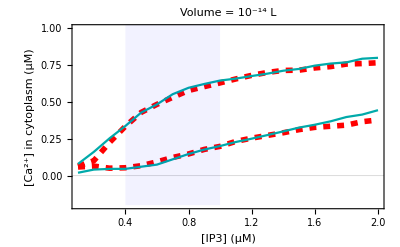
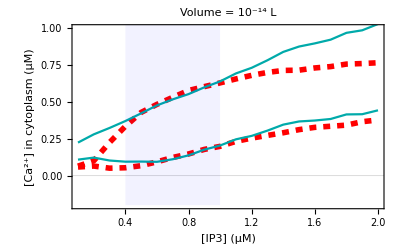
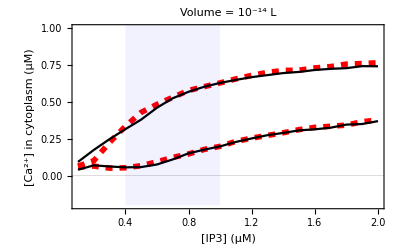
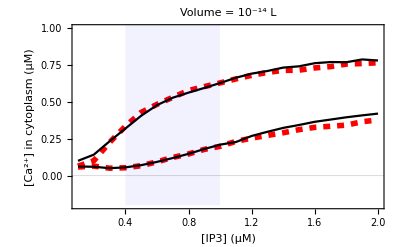
<|params_deep→-Graphics-,params_shallow→-Graphics-,rxns_deep→-Graphics-,rxns_shallow→-Graphics-|>

```mathematica
pltRes1=Association[];
Do[
pltRes1[mode]=Show[
{pltSS,plts[mode],pltOverlay},
PlotRange->{-0.2,1},
PlotLabel->"Volume = 10^-14 L",
FrameLabel->{"[IP3] (μM)","[Ca^(2+)] in cytoplasm (μM)"}]
,{mode,modesRun}]

pltRes1
```

# Range of oscillation diagrams average over many

## Plot SS

```mathematica
ip3sTrainVals=Table[pStrToNo[x],{x,ip3sTrain}];
pltOverlay=Graphics[{Opacity[0.05],Blue,Rectangle[{Min[ip3sTrainVals],-0.2},{Max[ip3sTrainVals],1.2}]}];
```

```mathematica
SetDirectory[NotebookDirectory[]<>"oscillation_range_data"];
ca2iMinMaxSS=Import["vol_14_no_ip3r_100.txt","Table"];

ca2iMinSS=Association[];
ca2iMaxSS=Association[];
Do[
ca2iMinSS[x[[1]]]=x[[2]];(*Around[x[[2]],x[[3]]];*)
ca2iMaxSS[x[[1]]]=x[[4]];(*Around[x[[4]],x[[5]]];*)
,{x,ca2iMinMaxSS}];

pltSS=ListLinePlot[{
Transpose[{Keys[ca2iMinSS],Values[ca2iMinSS]}],
Transpose[{Keys[ca2iMaxSS],Values[ca2iMaxSS]}]
},PlotStyle->{{Red}},PlotRange->{0,1}];
```

```mathematica
(*Dashed,Red,Thickness[0.01]*)
```

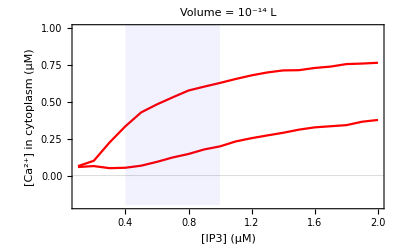

```mathematica
pEmpty=Show[pltSS,pltOverlay,PlotRange->{-0.2,1},
FrameLabel->{"[IP3] (μM)","[Ca^(2+)] in cytoplasm (μM)"},PlotLabel->"Volume = 10^-14 L"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/ss_learn_empty.pdf",pEmpty]
```

figures/ss_learn_empty.pdf

## Calculate

```mathematica
modesRun={"params_deep","rxns_deep","params_shallow","rxns_shallow"};
runStart=1;
runEnd=10;

Do[
Print[mode];

Monitor[
Do[

(* Import *)
SetDirectory[NotebookDirectory[]];
paramsSt=Import["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_params_integrated.mx"];

maxCa2i=Association[];
minCa2i=Association[];

Monitor[
Do[
ip3Integrate=ip3s[[idx]];
{muvC,stdvC}=getMeanStd[nv,nh,mv,sv,outMean[modePR[mode]],outStd[modePR[mode]],paramsSt[ip3Integrate]];
ca2iUpper=Transpose[muvC+stdvC][[1]];
ca2iLower=Transpose[muvC-stdvC][[1]];

maxCa2i[ip3Integrate]=Max[ca2iUpper[[-300;;]]];
minCa2i[ip3Integrate]=Min[ca2iLower[[-300;;]]];
,{idx,Length[ip3s]}];
,ProgressIndicator[idx,{1,Length[ip3s]}]];

SetDirectory[NotebookDirectory[]];
Export["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_min_ca2i.mx",minCa2i];
Export["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_max_ca2i.mx",maxCa2i];

,{iNet,runStart,runEnd}];
,ProgressIndicator[iNet,{runStart,runEnd}]];

,{mode,modesRun}];
```

params_deep

$Aborted

## Plot

```mathematica
modesRun={"params_deep","params_shallow","rxns_deep","rxns_shallow"};
runStart=1;
runEnd=10;

maxCa2i=Association[];
minCa2i=Association[];
Do[
maxCa2i[mode]=Association[];
minCa2i[mode]=Association[];

Do[

SetDirectory[NotebookDirectory[]];
maxCa2i[mode][iNet]=Values[Import["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_max_ca2i.mx"]];
minData=Import["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_min_ca2i.mx"];
minCa2i[mode][iNet]=Values[minData];
ip3Vals=Keys[minData];
,{iNet,runStart,runEnd}];
,{mode,modesRun}];

ip3Vals=pStrToNo@ip3Vals;
```

## V1

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);

c1=Darker[Cyan];
c2=Black;

colorsPlt=<|
"params_deep"->Directive[c1],
"rxns_deep"->Directive[c2],
"params_shallow"->Directive[c1],
"rxns_shallow"->Directive[c2]
|>;

colorsPltErr=<|
"params_deep"->Directive[c1,"LineOpacity"->0.8],
"rxns_deep"->Directive[c2,"LineOpacity"->0.8],
"params_shallow"->Directive[c1,"LineOpacity"->0.8],
"rxns_shallow"->Directive[c2,"LineOpacity"->0.8]
|>;

pltAve=Association[];
pltAveWithErr1=Association[];
pltAveWithErr2=Association[];

Do[
maxMean=Mean[Values[maxCa2i[mode]]];
maxStd=StandardDeviation[Values[maxCa2i[mode]]];
maxCI=1.96*maxStd/Sqrt[Length[Values[maxCa2i[mode]]]];
minMean=Mean[Values[minCa2i[mode]]];
minStd=StandardDeviation[Values[minCa2i[mode]]];
minCI=1.96*minStd/Sqrt[Length[Values[minCa2i[mode]]]];

maxUpper=Transpose[{ip3Vals,maxMean+maxCI}];
maxLower=Transpose[{ip3Vals,maxMean-maxCI}];
minUpper=Transpose[{ip3Vals,minMean+minCI}];
minLower=Transpose[{ip3Vals,minMean-minCI}];

maxMeanWithErr=Table[Around[maxMean[[i]],maxCI[[i]]],{i,Length[maxMean]}];
minMeanWithErr=Table[Around[minMean[[i]],minCI[[i]]],{i,Length[minMean]}];

pltAve[mode]=ListLinePlot[{Transpose[{ip3Vals,maxMean}],Transpose[{ip3Vals,minMean}]},PlotStyle->colorsPlt[mode],PlotRange->All];
pltAveWithErr1[mode]=ListPlot[Transpose[{ip3Vals,maxMeanWithErr}],PlotStyle->colorsPltErr[mode],PlotRange->All,IntervalMarkers->"Bars",PlotMarkers->{Automatic,PointSize[0.03]}];
pltAveWithErr2[mode]=ListPlot[Transpose[{ip3Vals,minMeanWithErr}],PlotStyle->colorsPltErr[mode],PlotRange->All,IntervalMarkers->"Bars",PlotMarkers->{Automatic,PointSize[0.03]}];
,{mode,modesRun}];
```

```mathematica
pltRes2=Association[];
pltRes2["deep"]=Show[
{pltSS,pltAveWithErr1["params_deep"],pltAveWithErr1["rxns_deep"],pltAveWithErr2["params_deep"],pltAveWithErr2["rxns_deep"],pltAve["params_deep"],pltAve["rxns_deep"],pltOverlay},
PlotRange->{-0.2,1},
FrameLabel->{"[IP3] (μM)","[Ca^(2+)] in cytoplasm (μM)"}];
pltRes2["shallow"]=Show[
{pltSS,pltAveWithErr1["params_shallow"],pltAveWithErr1["rxns_shallow"],pltAveWithErr2["params_shallow"],pltAveWithErr2["rxns_shallow"],pltAve["params_shallow"],pltAve["rxns_shallow"],pltOverlay},
PlotRange->{-0.2,1},
FrameLabel->{"[IP3] (μM)","[Ca^(2+)] in cytoplasm (μM)"}];

pltRes2
```

<|deep→-Graphics-,shallow→-Graphics-|>

```mathematica
leg=LineLegend[{Red,Black,Darker[Cyan]},{"# IP3R = 100\nStochastic\nsimulations","# IP3R = 100\nDBD (rxns)","# IP3R = 100\nDBD (params)"},LabelStyle->Directive[FontSize->24],LegendMarkerSize->40]
```

## Export data

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["oscillation_range_data"],CreateDirectory["oscillation_range_data"]];

Do[
maxMean=Mean[Values[maxCa2i[mode]]];
maxStd=StandardDeviation[Values[maxCa2i[mode]]];
minMean=Mean[Values[minCa2i[mode]]];
minStd=StandardDeviation[Values[minCa2i[mode]]];

dataWrite=Transpose[{ip3Vals,maxMean,maxStd,minMean,minStd}];
Export["oscillation_range_data/"<>mode<>".txt",dataWrite,"Table","Delimiter"->" "]
,{mode,Keys[maxCa2i]}];
```

## Export v1

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/bif_deep.pdf",pltRes2["deep"]]
Export["figures/bif_deep.png",pltRes2["deep"],ImageResolution->200]

Export["figures/bif_shallow.pdf",pltRes2["shallow"]]
Export["figures/bif_shallow.png",pltRes2["shallow"],ImageResolution->200]

Export["figures/leg.pdf",leg]
Export["figures/leg.png",leg,ImageResolution->200]
```

figures/bif_deep.pdf

figures/bif_deep.png

figures/bif_shallow.pdf

figures/bif_shallow.png

figures/leg.pdf

figures/leg.png

## V2 plots

```mathematica
colors=(("DefaultPlotStyle"/. (Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);

c1=Darker[Cyan];
c2=Black;

colorsPlt=<|
"params_deep"->Directive[c1],
"rxns_deep"->Directive[c2],
"params_shallow"->Directive[c1],
"rxns_shallow"->Directive[c2]
|>;
(*
colorsPltErr=<|
"params_deep"->Directive[Darker[Cyan],"LineOpacity"->0.3],
"rxns_deep"->Directive[Black,"LineOpacity"->0.3],
"params_shallow"->Directive[Darker[Cyan],"LineOpacity"->0.3],
"rxns_shallow"->Directive[Black,"LineOpacity"->0.3]
|>;
*)
colorsPltErr=<|
"params_deep"->Directive[c1,Dashed],
"rxns_deep"->Directive[c2,Dashed],
"params_shallow"->Directive[c1],
"rxns_shallow"->Directive[c2]
|>;
colorsShade=<|
"params_deep"->Directive[Opacity[0.1],c1],
"rxns_deep"->Directive[Opacity[0.2],c2],
"params_shallow"->Directive[Opacity[0.1],c1],
"rxns_shallow"->Directive[Opacity[0.2],c2]
|>;

pltAveBound=Association[];
pltAve=Association[];
pltAveDotUpper=Association[];
pltAveDotLower=Association[];
pltAveRangeMax=Association[];
pltAveRangeMin=Association[];
pltAveWithErr=Association[];

Do[
maxMean=Mean[Values[maxCa2i[mode]]];
maxStd=StandardDeviation[Values[maxCa2i[mode]]];
maxCI=1.96*maxStd/Sqrt[Length[Values[maxCa2i[mode]]]];
minMean=Mean[Values[minCa2i[mode]]];
minStd=StandardDeviation[Values[minCa2i[mode]]];
minCI=1.96*minStd/Sqrt[Length[Values[minCa2i[mode]]]];

maxUpper=Transpose[{ip3Vals,maxMean+maxCI}];
maxLower=Transpose[{ip3Vals,maxMean-maxCI}];
minUpper=Transpose[{ip3Vals,minMean+minCI}];
minLower=Transpose[{ip3Vals,minMean-minCI}];

maxMeanWithErr=Table[Around[maxMean[[i]],maxCI[[i]]],{i,Length[maxMean]}];
minMeanWithErr=Table[Around[minMean[[i]],minCI[[i]]],{i,Length[minMean]}];

pltAveBound[mode]=ListLinePlot[{maxUpper,maxLower,minUpper,minLower},PlotStyle->LightGray,PlotRange->All];
pltAve[mode]=ListLinePlot[{Transpose[{ip3Vals,maxMean}],Transpose[{ip3Vals,minMean}]},PlotStyle->colorsPlt[mode],PlotRange->All];
pltAveDotUpper[mode]=ListPlot[Transpose[{ip3Vals,maxMean}],PlotStyle->colorsPlt[mode],PlotRange->All,PlotMarkers->{Automatic,PointSize[0.03]}];
pltAveDotLower[mode]=ListPlot[Transpose[{ip3Vals,minMean}],PlotStyle->colorsPlt[mode],PlotRange->All,PlotMarkers->{Automatic,PointSize[0.03]}];
pltAveRangeMax[mode]=ListLinePlot[{maxLower,maxUpper},PlotStyle->Opacity[0],PlotRange->All,Filling->{1->{{2},{colorsShade[mode],White}}}];
pltAveRangeMin[mode]=ListLinePlot[{minLower,minUpper},PlotStyle->Opacity[0],PlotRange->All,Filling->{1->{{2},{colorsShade[mode],White}}}];
pltAveWithErr[mode]=ListPlot[{Transpose[{ip3Vals,maxMeanWithErr}],Transpose[{ip3Vals,minMeanWithErr}]},PlotStyle->colorsPltErr[mode],PlotRange->All,IntervalMarkers->"Bars",PlotMarkers->{Automatic,PointSize[0.03]}]
,{mode,modesRun}];
```

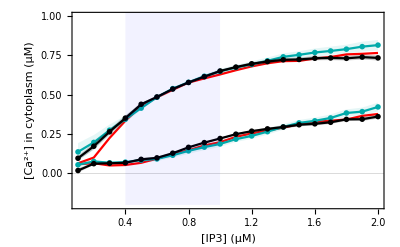
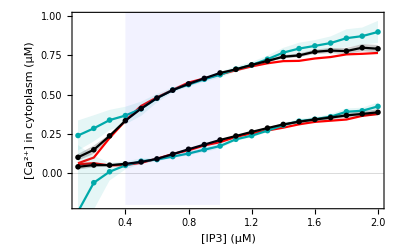
<|deep→-Graphics-,shallow→-Graphics-|>

```mathematica
pltRes3=Association[];
pltRes3["deep"]=Show[
{pltSS,pltAveRangeMin["params_deep"],pltAveRangeMax["params_deep"],pltAve["params_deep"],pltAveDotUpper["params_deep"],pltAveDotLower["params_deep"],pltAveRangeMin["rxns_deep"],pltAveRangeMax["rxns_deep"],pltAve["rxns_deep"],pltAveDotUpper["rxns_deep"],pltAveDotLower["rxns_deep"],pltOverlay},
PlotRange->{-0.2,1},
FrameLabel->{"[IP3] (μM)","[Ca^(2+)] in cytoplasm (μM)"}];
pltRes3["shallow"]=Show[
{pltSS,pltAveRangeMin["params_shallow"],pltAveRangeMax["params_shallow"],pltAve["params_shallow"],pltAveDotUpper["params_shallow"],pltAveDotLower["params_shallow"],pltAveRangeMin["rxns_shallow"],pltAveRangeMax["rxns_shallow"],pltAve["rxns_shallow"],pltAveDotUpper["rxns_shallow"],pltAveDotLower["rxns_shallow"],pltOverlay},
PlotRange->{-0.2,1},
FrameLabel->{"[IP3] (μM)","[Ca^(2+)] in cytoplasm (μM)"}];

pltRes3
```

## Export v2

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/bif_deep_v2.pdf",pltRes3["deep"]]
Export["figures/bif_deep_v2.png",pltRes3["deep"],ImageResolution->200]

Export["figures/bif_shallow_v2.pdf",pltRes3["shallow"]]
Export["figures/bif_shallow_v2.png",pltRes3["shallow"],ImageResolution->200]
```

figures/bif_deep_v2.pdf

figures/bif_deep_v2.png

figures/bif_shallow_v2.pdf

figures/bif_shallow_v2.png

# Integrate

```mathematica
pltsAll=Association[];
Do[
pltsAll[k]=ListLinePlot[
Table[
filtered0[ip3]["LFDL"][k]
,{ip3,Join[ip3sTrain,ip3sTest]}]
,PlotStyle->Gray,PlotRange->All]
,{k,makeLF[nv,nh]}]
```

```mathematica
ip3sTest
ip3sTrain
```

{ip3_0p100,ip3_0p200,ip3_0p300,ip3_1p100,ip3_1p200,ip3_1p300,ip3_1p400,ip3_1p500,ip3_1p600,ip3_1p700,ip3_1p800,ip3_1p900,ip3_2p000}

{ip3_0p400,ip3_0p500,ip3_0p600,ip3_0p700,ip3_0p800,ip3_0p900,ip3_1p000}

```mathematica
iNet=2;
modesRun={"params_deep","params_shallow","rxns_deep","rxns_shallow"};

(* Import *)
SetDirectory[NotebookDirectory[]];
paramsIntegrated=Association[];
Do[
paramsIntegrated[mode]=Import["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_params_integrated.mx"];
,{mode,modesRun}];
```

```mathematica
Keys[dataDesc]
```

{noSeeds,volExp,noIP3R,tptStart,tptMax,tptInterval,tpts,times,noTpts}

```mathematica
labels=<|"ip3_0p300"->"[IP_3] = 0.3μM","ip3_0p700"->"[IP_3] = 0.7μM"|>
```

<|ip3_0p300→[IP_3] = 0.3μM,ip3_0p700→[IP_3] = 0.7μM|>

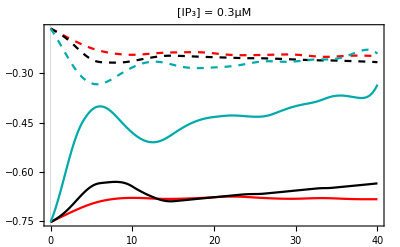
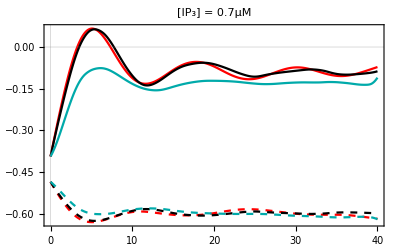

Solid lines: b_1         Dashed lines: W_11

```mathematica
ip3sPlt={"ip3_0p300","ip3_0p700"};
modesPlt={"rxns_shallow","params_shallow"};
timesPlt=dataDesc["times"]-dataDesc["times"][[1]];

{p3,p7}=Table[
f=Table[Transpose[{timesPlt,filtered0[ip3]["LFDL"][k]}],{k,{"wt11","b1"}}];
p=Flatten[Table[Table[Transpose[{timesPlt,paramsIntegrated[mode][ip3]["LFDL"][k][[;;-2]]}],{k,{"wt11","b1"}}],{mode,modesPlt}],1];
fl={"Time (s)"};

Show[
ListLinePlot[f,PlotStyle->{Directive[Red,Dashed],Directive[Red]},PlotRange->All],
ListLinePlot[p,PlotStyle->{Directive[Black,Dashed],Directive[Black],Directive[Darker[Cyan],Dashed],Directive[Darker[Cyan]]},PlotRange->All],
PlotLabel->labels[ip3],
PlotRange->All,
FrameLabel->fl
]
,{ip3,ip3sPlt}]

leg1=LineLegend[{Red,Black,Darker[Cyan]},{"Data","DBD (rxns)","DBD (params)"},LegendLayout->"Row"]
leg2=Style[Text["Solid lines: b_1         Dashed lines: W_11"],FontSize->24]
```

## Export

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/ex_ip3_0p300.pdf",p3]
Export["figures/ex_ip3_0p300.png",p3,ImageResolution->200]

Export["figures/ex_ip3_0p700.pdf",p7]
Export["figures/ex_ip3_0p700.png",p7,ImageResolution->200]

Export["figures/ex_leg_1.pdf",leg1]
Export["figures/ex_leg_1.png",leg1,ImageResolution->200]

Export["figures/ex_leg_2.pdf",leg2]
Export["figures/ex_leg_2.png",leg2,ImageResolution->200]
```

figures/ex_ip3_0p300.pdf

figures/ex_ip3_0p300.png

figures/ex_ip3_0p700.pdf

figures/ex_ip3_0p700.png

figures/ex_leg_1.pdf

figures/ex_leg_1.png

figures/ex_leg_2.pdf

figures/ex_leg_2.png

## Plot single

<|{ip3_1p300,wt11}→W_(Ca, X) at [IP_3] = 1.3μM,{ip3_0p700,b1}→b_Ca at [IP_3] = 0.7μM|>

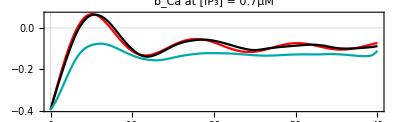
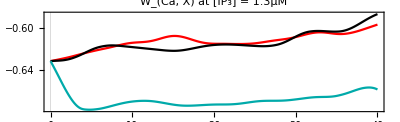

```mathematica
ip3sPlt={{"ip3_0p700","b1"},{"ip3_1p300","wt11"}};
modesPlt={"rxns_shallow","params_shallow"};
timesPlt=dataDesc["times"]-dataDesc["times"][[1]];

labels=<|{"ip3_1p300","wt11"}->"W_(Ca, X) at [IP_3] = 1.3μM",{"ip3_0p700","b1"}->"b_Ca at [IP_3] = 0.7μM"|>

{p7,p13}=Table[
{ip3,k}=x;
f=Transpose[{timesPlt,filtered0[ip3]["LFDL"][k]}];
p=Table[Transpose[{timesPlt,paramsIntegrated[mode][ip3]["LFDL"][k][[;;-2]]}],{mode,modesPlt}];
fl={"Time (s)"};

Show[
ListLinePlot[f,PlotStyle->{Directive[Red]},PlotRange->All],
ListLinePlot[p,PlotStyle->{Directive[Black],Directive[Darker[Cyan]]},PlotRange->All],
PlotLabel->labels[x],
PlotRange->All,
FrameLabel->fl,
AspectRatio->0.305
]
,{x,ip3sPlt}]

leg1=LineLegend[{Red},{"Data"},LegendLayout->"Row"]
leg2=LineLegend[{Black,Darker[Cyan]},{"DBD (rxns)","DBD (params)"}]
```

## Export

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/ex_single_ip3_1p300.pdf",p13]
Export["figures/ex_single_ip3_1p300.png",p13,ImageResolution->200]

Export["figures/ex_single_ip3_0p700.pdf",p7]
Export["figures/ex_single_ip3_0p700.png",p7,ImageResolution->200]

Export["figures/ex_single_leg_1.pdf",leg1]
Export["figures/ex_single_leg_1.png",leg1,ImageResolution->200]
```

figures/ex_single_ip3_1p300.pdf

figures/ex_single_ip3_1p300.png

figures/ex_single_ip3_0p700.pdf

figures/ex_single_ip3_0p700.png

figures/ex_single_leg_1.pdf

figures/ex_single_leg_1.png

# MSE error

```mathematica
modesRun={"params_deep","params_shallow","rxns_deep","rxns_shallow"};
noRun=10;
mse=Association[];

SetDirectory[NotebookDirectory[]];
Do[
mse[mode]=Association[];
Do[
mse[mode][iNet]=Association[];
paramsIntegrated=Import["trained/"<>mode<>"/"<>IntegerString[iNet,10,2]<>"_params_integrated.mx"];
Do[

mse[mode][iNet][ip3]=0.0;
count=0;
Do[
true=filtered0[ip3]["LFDL"][k];
int=paramsIntegrated[ip3]["LFDL"][k][[;;-2]];
mse[mode][iNet][ip3]+=Total[(int-true)^2];
count+=Length[int];
,{k,{"b1","wt11"}}];

mse[mode][iNet][ip3]=mse[mode][iNet][ip3]/count;
,{ip3,ip3s}];
,{iNet,noRun}];
,{mode,modesRun}];
```

```mathematica
motif1=Graphics[{Darker[Cyan],Opacity[0.15],Thickness[0.025],Line[Table[{{k,-1},{k+1,1}},{k,-2,2,.1}]]},PlotRange-> 1];
motif2=Graphics[{Gray,Opacity[0.2],Thickness[0.025],Line[Table[{{k,1},{k+1,-1}},{k,-2,2,.1}]]},PlotRange-> 1];
```

```mathematica
(*
dx=0.2;
recs=Flatten[Table[Table[Rectangle[{k1,k2},{k1+0.5*dx,k2+0.5*dx}],{k1,-2,2,dx}],{k2,-2,2,dx}],1];
motif1=Graphics[{Darker[Cyan],Opacity[0.2],Thickness[0.025],recs},PlotRange-> 1]
*)
```

```mathematica
mseWithErr=Association[];
mseWithoutErr=Association[];
mseUpperLog=Association[];
mseLowerLog=Association[];
Do[
mseWithErr[mode]=Association[];
mseWithoutErr[mode]=Association[];
mseUpperLog[mode]=Association[];
mseLowerLog[mode]=Association[];
Do[
vals=Table[mse[mode][iNet][ip3],{iNet,noRun}];
m=Mean[vals];
s=1.96*StandardDeviation[vals]/Sqrt[noRun];
mseWithErr[mode][ip3]=Around[m,s];
mseWithoutErr[mode][ip3]=m;
mseUpperLog[mode][ip3]=Max[m+s,10^(-10)];
mseLowerLog[mode][ip3]=Max[m-s,10^(-10)];
,{ip3,ip3s}];
,{mode,modesRun}];
```

```mathematica
cols=<|
"params_shallow"->Directive[Opacity[0.08],Darker[Cyan]],
"rxns_shallow"->Directive[Opacity[0.2],Gray],
"params_deep"->Directive[Opacity[0.08],Darker[Cyan]],
"rxns_deep"->Directive[Opacity[0.2],Gray]
|>;
pShade=Association[];
Do[
valsPlt={
Transpose[{ip3Vals,Values[mseLowerLog[mode]]}],
Transpose[{ip3Vals,Values[mseUpperLog[mode]]}]
};

If[mode=="params_deep",
pShade[mode]=ListLogPlot[valsPlt,Filling->{1->{2}},FillingStyle->PatternFilling[motif1],PlotStyle->Directive["LineOpacity"->0],Joined->True,PlotRange->All]
];
If[mode=="rxns_deep",
pShade[mode]=ListLogPlot[valsPlt,Filling->{1->{2}},FillingStyle->PatternFilling[motif2],PlotStyle->Directive["LineOpacity"->0],Joined->True,PlotRange->All]
];
If[mode=="params_shallow"||mode=="rxns_shallow",
pShade[mode]=ListLogPlot[valsPlt,Filling->{1->{{2},{cols[mode],White}}},PlotStyle->Directive["LineOpacity"->0],Joined->True,PlotRange->All]
];
,{mode,modesRun}];
```

```mathematica
(*
p1=Show[
pShade["params_shallow"],
pShade["rxns_shallow"],
ListLogPlot[{
Transpose[{ip3Vals,Values[mseWithoutErr["params_shallow"]]}],
Transpose[{ip3Vals,Values[mseWithoutErr["rxns_shallow"]]}]
},PlotStyle->{Directive[Darker[Cyan],Dashed],Directive[Black,Dashed],Darker[Cyan],Black},Joined->True]
];
p2=Show[
pShade["params_deep"],
pShade["rxns_deep"],
ListLogPlot[{
Transpose[{ip3Vals,Values[mseWithoutErr["params_deep"]]}],
Transpose[{ip3Vals,Values[mseWithoutErr["rxns_deep"]]}]
},PlotStyle->{Directive[Darker[Cyan],Dashed],Directive[Black,Dashed],Darker[Cyan],Black},Joined->True]
];
*)
```

```mathematica
ip3sTrainVals=Table[pStrToNo[x],{x,ip3sTrain}];
pltOverlay=Graphics[{Opacity[0.05],Blue,Rectangle[{Min[ip3sTrainVals],Log[10^-5]},{Max[ip3sTrainVals],Log[10]}]}];
```

```mathematica
pMSE=Show[
ListLogPlot[{},PlotRange->{{0,2.05},{5*10^-5,1}}],
pltOverlay,
pShade["params_deep"],
pShade["rxns_deep"],
pShade["params_shallow"],
pShade["rxns_shallow"],
ListLogPlot[{
Transpose[{ip3Vals,Values[mseWithoutErr["params_deep"]]}],
Transpose[{ip3Vals,Values[mseWithoutErr["rxns_deep"]]}]
},PlotStyle->{Directive[Darker[Cyan],Dashed],Directive[Black,Dashed],Darker[Cyan],Black},Joined->True,PlotRange->All],
ListLogPlot[{
Transpose[{ip3Vals,Values[mseWithoutErr["params_shallow"]]}],
Transpose[{ip3Vals,Values[mseWithoutErr["rxns_shallow"]]}]
},PlotStyle->{Directive[Darker[Cyan]],Directive[Black],Darker[Cyan],Black},Joined->True,PlotRange->All],
FrameLabel->{"[IP3] (μM)"},
PlotLabel->"MSE"
]
```

-Graphics-

```mathematica
leg=LineLegend[{Directive[Black,Thickness[0.008]],Directive[Darker[Cyan],Thickness[0.008]],Directive[Dashed,Black,Thickness[0.008]],Directive[Dashed,Darker[Cyan],Thickness[0.008]]},
{"Shallow subnet (rxns)","Shallow subnet (params)","Deep subnet (rxns)","Deep subnet (params)"},LegendLayout->"Row",LabelStyle->Directive[FontSize->24]]
```

```mathematica
leg1=LineLegend[{Directive[Darker[Cyan],Thickness[0.008]],Directive[Dashed,Darker[Cyan],Thickness[0.008]]},
{"Shallow subnet (params)","Deep subnet (params)"},LabelStyle->Directive[FontSize->24]]
```

```mathematica
leg2=LineLegend[{Directive[Black,Thickness[0.008]],Directive[Dashed,Black,Thickness[0.008]]},
{"Shallow subnet (rxns)","Deep subnet (rxns)"},LabelStyle->Directive[FontSize->24]]
```

## Export

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/mse.pdf",pMSE]
Export["figures/mse.png",pMSE,ImageResolution->200]
Export["figures/mse_leg.pdf",leg]
Export["figures/mse_leg.png",leg,ImageResolution->200]
Export["figures/mse_leg1.pdf",leg1]
Export["figures/mse_leg1.png",leg1,ImageResolution->200]
Export["figures/mse_leg2.pdf",leg2]
Export["figures/mse_leg2.png",leg2,ImageResolution->200]
```

figures/mse.pdf

figures/mse.png

figures/mse_leg.pdf

figures/mse_leg.png

figures/mse_leg1.pdf

figures/mse_leg1.png

figures/mse_leg2.pdf

figures/mse_leg2.png

# Plot learned muh, varh

```mathematica
fourier[offset_,sinCoeffs_,cosCoeffs_,freqs_,tptPlt_]:=Module[
{range,pts}
,
range=Max[Total[Abs[sinCoeffs]+Abs[cosCoeffs]]+10^-8,1];
pts=Table[offset[[1]]+(Sum[sinCoeffs[[i]]*Sin[freqs[[i]]*(tpt-1)]+cosCoeffs[[i]]*Cos[freqs[[i]]*(tpt-1)],{i,Length[freqs]}])/range,{tpt,tptPlt}];

Return[pts];
];
```

```mathematica
fourierMuh=Association[];
fourierVarh=Association[];
muhSinCoeffSt=Association[];
muhCosCoeffSt=Association[];
varhSinCoeffSt=Association[];
varhCosCoeffSt=Association[];

Do[

fourierMuh[mode]=Association[];
fourierVarh[mode]=Association[];
muhSinCoeffSt[mode]=Association[];
muhCosCoeffSt[mode]=Association[];
varhSinCoeffSt[mode]=Association[];
varhCosCoeffSt[mode]=Association[];

Do[
(* Import *)
SetDirectory[NotebookDirectory[]];
trained=Import["trained/"<>mode<>"/"<>IntegerString[iRun,10,2]<>".wlnet"];

(* Extract coeffs *)
arrs=Information[trained,"Arrays"];
muhOffset=Normal[arrs[{"inputsWOSTD","convert0","layerMuh","offset","Array"}]];
muhCosCoeff=Normal[arrs[{"inputsWOSTD","convert0","layerMuh","cosCoeff","Array"}]];
muhSinCoeff=Normal[arrs[{"inputsWOSTD","convert0","layerMuh","sinCoeff","Array"}]];
If[muhCosCoeff[[1]]<0,
muhCosCoeff*=-1;
muhSinCoeff*=-1;
];

muhSinCoeffSt[mode][iRun]=muhSinCoeff;
muhCosCoeffSt[mode][iRun]=muhCosCoeff;

varhOffset=Normal[arrs[{"inputsWOSTD","convert0","layerVarh","offset","Array"}]];
varhCosCoeff=
Normal[arrs[{"inputsWOSTD","convert0","layerVarh","cosCoeff","Array"}]];
varhSinCoeff=Normal[arrs[{"inputsWOSTD","convert0","layerVarh","sinCoeff","Array"}]];
If[varhCosCoeff[[1]]<0,
varhCosCoeff*=-1;
varhSinCoeff*=-1;
];

varhSinCoeffSt[mode][iRun]=varhSinCoeff;
varhCosCoeffSt[mode][iRun]=varhCosCoeff;

(* Plot *)
tptsPlt=Table[tpt,{tpt,1,dataDesc["noTpts"]}];
fourierMuh[mode][iRun]=fourier[muhOffset,muhSinCoeff,muhCosCoeff,freqs[modePR[mode]],tptsPlt];
fourierVarh[mode][iRun]=fourier[varhOffset,varhSinCoeff,varhCosCoeff,freqs[modePR[mode]],tptsPlt];
,{iRun,20}];
,{mode,{"params_deep","rxns_deep","params_shallow","rxns_shallow"}}];
```

```mathematica
makePlt[fourier_,mode_,rng_,showFrame_]:=Module[
{plt,pts,fl}
,
If[showFrame,
fl={"Time (s)"},
fl=None
];

plt=Show[
pts=Table[fourier[mode][iRun],{iRun,20}];
pts=Table[Transpose[{dataDesc["times"]-dataDesc["times"][[1]],pt}],{pt,pts}];
ListLinePlot[pts,PlotRange->All,PlotStyle->Darker[LightGray,0.05]],
ListLinePlot[Mean[pts],PlotRange->All,PlotStyle->colors[modePR[mode]]],
PlotLabel->labels[mode],
FrameLabel->fl,
PlotRange->rng
];
Return[plt]
];
```

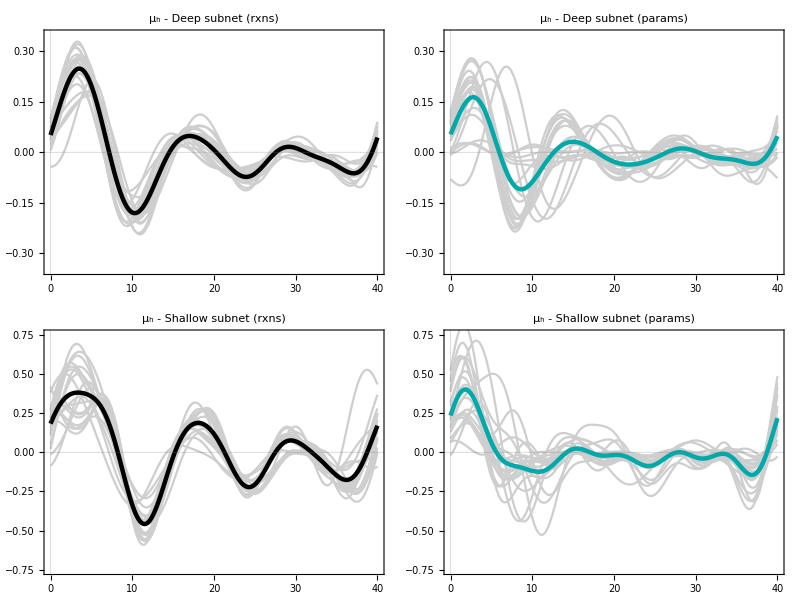

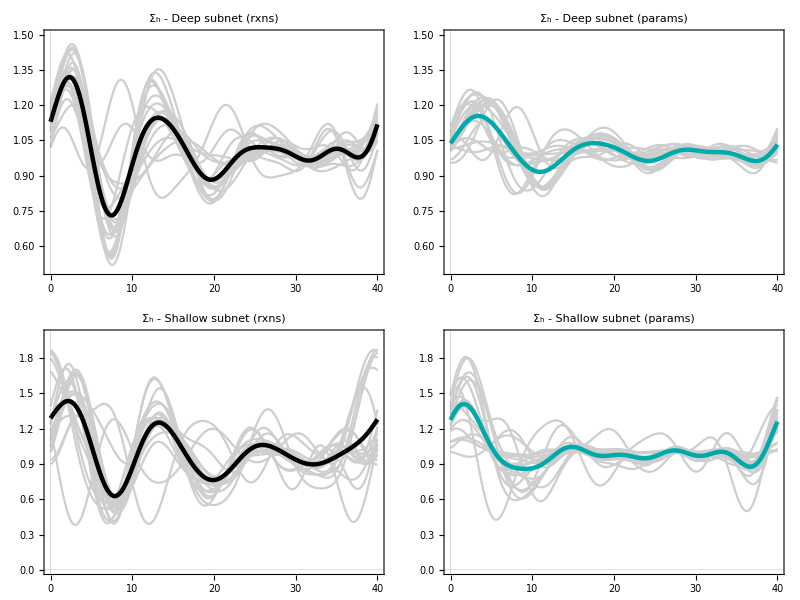

```mathematica
colors=<|
"params"->Directive[Darker[Cyan],Thickness[0.008]],
"rxns"->Directive[Black,Thickness[0.008]]
|>;
labels=<|
"params_deep"->"μ_h - Deep subnet (params)",
"rxns_deep"->"μ_h - Deep subnet (rxns)",
"params_shallow"->"μ_h - Shallow subnet (params)",
"rxns_shallow"->"μ_h - Shallow subnet (rxns)"
|>;

pltsMuh=Association[];
Do[
If[mode=="rxns_deep"||mode=="params_deep",
pltsMuh[mode]=makePlt[fourierMuh,mode,{-0.35,0.35},False],
pltsMuh[mode]=makePlt[fourierMuh,mode,{-0.75,0.75},True]
]
,{mode,{"rxns_deep","params_deep","rxns_shallow","params_shallow"}}];

labels=<|
"params_deep"->"Σ_h - Deep subnet (params)",
"rxns_deep"->"Σ_h - Deep subnet (rxns)",
"params_shallow"->"Σ_h - Shallow subnet (params)",
"rxns_shallow"->"Σ_h - Shallow subnet (rxns)"
|>;

pltsVarh=Association[];
Do[
If[mode=="rxns_deep"||mode=="params_deep",
pltsVarh[mode]=makePlt[fourierVarh,mode,{0.5,1.5},False],
pltsVarh[mode]=makePlt[fourierVarh,mode,{0,2},True]
]
,{mode,{"rxns_deep","params_deep","rxns_shallow","params_shallow"}}];

leg=LineLegend[Join[Reverse[Values[colors]],{Darker[LightGray,0.05]}],{"Mean (rxns)","Mean (params)","Trained models"},LegendLayout->"Row"]
leg2=LineLegend[Join[Reverse[Values[colors]],{Darker[LightGray,0.05]}],{"Mean (rxns)","Mean (params)","Trained models"}]

SetDirectory[NotebookDirectory[]];
Export["figures/fourier/leg.pdf",leg];
Export["figures/fourier/leg2.pdf",leg2];
Do[
Export["figures/fourier/muh_"<>mode<>".pdf",pltsMuh[mode]];
Export["figures/fourier/varh_"<>mode<>".pdf",pltsVarh[mode]];
,{mode,Keys[pltsMuh]}]

(*
Grid[{{
Show[pltsMuh["rxns_deep"],pltsVarh["rxns_deep"],PlotRange->All],
Show[pltsMuh["params_deep"],pltsVarh["params_deep"],PlotRange->All]
},{
Show[pltsMuh["rxns_shallow"],pltsVarh["rxns_shallow"],PlotRange->All],
Show[pltsMuh["params_shallow"],pltsVarh["params_shallow"],PlotRange->All]
}}]
*)

Grid[ArrayReshape[Values[pltsMuh],{2,2}]]
Grid[ArrayReshape[Values[pltsVarh],{2,2}]]
```

## Check positive definite

```mathematica
ip3="ip3_0p400";
paramsF=filtered0[ip3]["LD"];
mode="params_deep";
iNet=10;

Do[
x=paramsF[[tpt]];
x["muh"]={fourierMuh[mode][iNet][[tpt]]};
x["varh"]={{fourierVarh[mode][iNet][[tpt]]}};
paramsF[[tpt]]=x;
,{tpt,Length[paramsF]}];
momentsF=Table[convertParamsToMoments[nv,x],{x,paramsF}];
```

```mathematica
Table[PositiveDefiniteMatrixQ[x["var"]],{x,momentsF}]==ConstantArray[True,Length[momentsF]]
```

True

## Jacobian Funcs

```mathematica
makeConvertParams0ToParamsLayerLATENT[]:=Module[
{layerDefns,layerConn,graph}
,
layerDefns=<|
"convertblayer"->convertbLayerFrom0[],
"flattenb"->FlattenLayer[],
"convertwtlayer"->convertwtLayerFrom0[]
|>;

layerConn={
NetPort["muh"]->NetPort["convertblayer","muh2"],
NetPort["varh"]->NetPort["convertblayer","varh2"],
"convertblayer"->"flattenb"->NetPort["b2"],

NetPort["varh"]->NetPort["convertwtlayer","varh2"],
"convertwtlayer"->NetPort["wt2"],

NetPort["muh"]->NetPort["muh2"],
NetPort["varh"]->NetPort["varh2"],
NetPort["sig2"]->NetPort["sig2"]
};

graph=NetGraph[layerDefns,layerConn,"sig2"->1,"muh"->{1},"varh"->{1,1}];
Return[graph]
]
```

```mathematica
makeGraphInputsWOSTDLATENTrxns[nv_,nh_,rxnSpecs_]:=Module[
{layerDefns,layerConn,graph,rxnName,idx}
,
layerDefns=<|
"convert0"->makeConvertParams0ToParamsLayerLATENT[],
"rxnsCatenate"->CatenateLayer[]
|>;

layerConn={
NetPort["wt"]->NetPort["convert0","wt1"],
NetPort["b"]->NetPort["convert0","b1"]
};

(* Reactions *)
idx=1;
Monitor[
Do[
rxnName="rxn"<>ToString[idx];
idx+=1;

layerDefns[rxnName]=makeRxnParams0TEflat[nv,nh,rxnSpec];

layerConn=Join[layerConn,{
NetPort["convert0","wt2"]->NetPort[rxnName,"wt"],
NetPort["convert0","b2"]->NetPort[rxnName,"b"],
NetPort["convert0","sig2"]->NetPort[rxnName,"sig2"],
NetPort["convert0","muh2"]->NetPort[rxnName,"muh"],
NetPort["convert0","varh2"]->NetPort[rxnName,"varh"],
rxnName->"rxnsCatenate"
}];
,{rxnSpec,rxnSpecs}];
,ProgressIndicator[idx,{1,Length[rxnSpecs]}]];

Return[NetGraph[layerDefns,layerConn]];
]
```

```mathematica
makeGraphInputsWOSTDLATENTparams[nv_,nh_]:=Module[
{layerDefns,layerConn,graph,rxnName,idx}
,
layerDefns=<|
"convert0"->makeConvertParams0ToParamsLayerLATENT[],
"catenate"->CatenateLayer[],
"wt2Flatten"->FlattenLayer[],
"varh2Flatten"->FlattenLayer[]
|>;

layerConn={
NetPort["wt"]->NetPort["convert0","wt1"],
NetPort["b"]->NetPort["convert0","b1"],

NetPort["convert0","wt2"]->"wt2Flatten"->"catenate",
NetPort["convert0","varh2"]->"varh2Flatten"->"catenate",
NetPort["convert0","sig2"]->"catenate",
NetPort["convert0","muh2"]->"catenate",
NetPort["convert0","b2"]->"catenate"
};

Return[NetGraph[layerDefns,layerConn]];
]
```

## Fourier coeffs. convergence

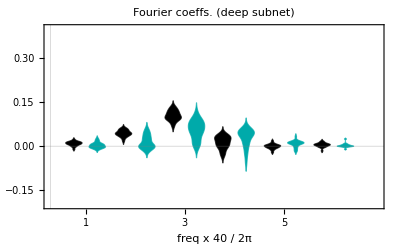
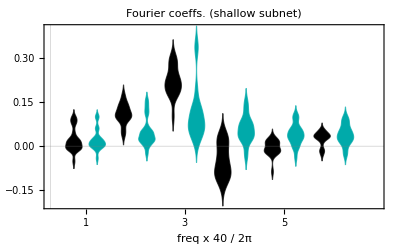
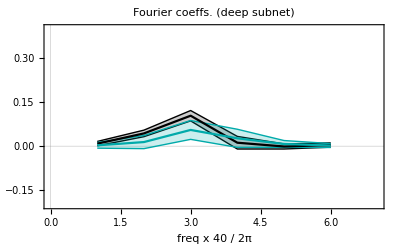
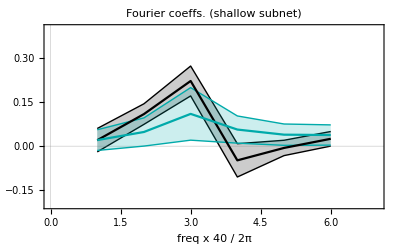
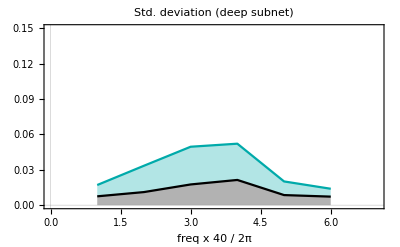
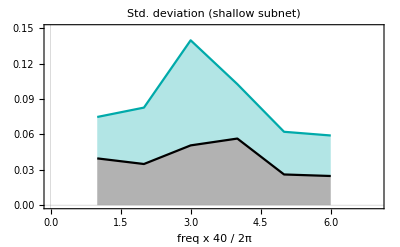
| 
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
flabels={"freq x 40 / 2π"};

valsRxnsDeep=Transpose[Values[muhSinCoeffSt["rxns_deep"]]];
valsParamsDeep=Transpose[Values[muhSinCoeffSt["params_deep"]]];
valsDeep=Transpose[{valsRxnsDeep,valsParamsDeep}];

valsRxnsShallow=Transpose[Values[muhSinCoeffSt["rxns_shallow"]]];
valsParamsShallow=Transpose[Values[muhSinCoeffSt["params_shallow"]]];
valsShallow=Transpose[{valsRxnsShallow,valsParamsShallow}];

rng={{0,14},{-0.2,0.4}};
pD1=DistributionChart[valsDeep,ImageSize->400,PlotRange->rng,FrameLabel->flabels,BaseStyle->Directive[FontSize->24],PlotTheme->"Scientific",ChartLabels->{{1,2,3,4,5,6},None},PlotLabel->"Fourier coeffs. (deep subnet)",ChartStyle->{Black,Darker[Cyan]}];
pD2=DistributionChart[valsShallow,ImageSize->400,PlotRange->rng,FrameLabel->flabels,BaseStyle->Directive[FontSize->24],PlotTheme->"Scientific",ChartLabels->{{1,2,3,4,5,6},None},PlotLabel->"Fourier coeffs. (shallow subnet)",ChartStyle->{Black,Darker[Cyan]}];

meanRxnsDeep=Mean[Transpose[valsRxnsDeep]];
stdRxnsDeep=StandardDeviation[Transpose[valsRxnsDeep]];
rxnsDeep=Table[Around[meanRxnsDeep[[i]],stdRxnsDeep[[i]]],{i,Length[meanRxnsDeep]}];

meanParamsDeep=Mean[Transpose[valsParamsDeep]];
stdParamsDeep=StandardDeviation[Transpose[valsParamsDeep]];
paramsDeep=Table[Around[meanParamsDeep[[i]],stdParamsDeep[[i]]],{i,Length[meanParamsDeep]}];

meanRxnsShallow=Mean[Transpose[valsRxnsShallow]];
stdRxnsShallow=StandardDeviation[Transpose[valsRxnsShallow]];
rxnsShallow=Table[Around[meanRxnsShallow[[i]],stdRxnsShallow[[i]]],{i,Length[meanRxnsShallow]}];

meanParamsShallow=Mean[Transpose[valsParamsShallow]];
stdParamsShallow=StandardDeviation[Transpose[valsParamsShallow]];
paramsShallow=Table[Around[meanParamsShallow[[i]],stdParamsShallow[[i]]],{i,Length[meanParamsShallow]}];

rng={{0,7},{-0.2,0.4}};
pL1=ListLinePlot[{rxnsDeep,paramsDeep},IntervalMarkers->"Bands",PlotRange->rng,FrameLabel->flabels,PlotLabel->"Fourier coeffs. (deep subnet)",PlotStyle->{Black,Darker[Cyan]}];
pL2=ListLinePlot[{rxnsShallow,paramsShallow},IntervalMarkers->"Bands",PlotRange->rng,FrameLabel->flabels,PlotLabel->"Fourier coeffs. (shallow subnet)",PlotStyle->{Black,Darker[Cyan]}];

rng={{0,7},{-0.02,0.14}};
pL1close=ListLinePlot[{rxnsDeep,paramsDeep},IntervalMarkers->"Bands",PlotRange->rng,FrameLabel->flabels,PlotLabel->"Fourier coeffs. (deep subnet)",PlotStyle->{Black,Darker[Cyan]}];

rng={{0,7},{0,0.15}};
pS1=StackedListPlot[
{stdRxnsDeep,stdParamsDeep},
ImageSize->400,PlotRange->rng,FrameLabel->flabels,BaseStyle->Directive[FontSize->24],PlotTheme->"Scientific",PlotLabel->"Std. deviation (deep subnet)",PlotStyle->{Black,Darker[Cyan]}];
pS2=StackedListPlot[
{stdRxnsShallow,stdParamsShallow},
ImageSize->400,PlotRange->rng,FrameLabel->flabels,BaseStyle->Directive[FontSize->24],PlotTheme->"Scientific",PlotLabel->"Std. deviation (shallow subnet)",PlotStyle->{Black,Darker[Cyan]}];

rng={{0,7},{0,0.06}};
pS1close=StackedListPlot[
{stdRxnsDeep,stdParamsDeep},
ImageSize->400,PlotRange->rng,FrameLabel->flabels,BaseStyle->Directive[FontSize->24],PlotTheme->"Scientific",PlotLabel->"Std. deviation (deep subnet)",PlotStyle->{Black,Darker[Cyan]}];

leg=LineLegend[{Black,Darker[Cyan]},{"Reaction-based","Parameter-based"}];

p=Grid[{
{leg},
{pD1,pD2},
{pL1,pL2},
{pS1,pS2}
}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["figures/fourier_coeffs/conv.pdf",p];
Export["figures/fourier_coeffs/leg.pdf",leg];
Export["figures/fourier_coeffs/f_deep.pdf",pL1];
Export["figures/fourier_coeffs/f_shallow.pdf",pL2];
Export["figures/fourier_coeffs/std_deep.pdf",pS1];
Export["figures/fourier_coeffs/std_shallow.pdf",pS2];

Export["figures/fourier_coeffs/f_deep_close.pdf",pL1close];
Export["figures/fourier_coeffs/std_deep_close.pdf",pS1close];
```

## Plot freqs

```mathematica
freqs
```

<|params→{0.0156688,0.0313376,0.0470064,0.0626752,0.078344,0.0940127},rxns→{0.0156688,0.0313376,0.0470064,0.0626752,0.078344,0.0940127}|>

```mathematica
freqsR=freqs*dataDesc["noTpts"]/(2*Pi)
```

<|params→{1.,2.,3.,4.,5.,6.},rxns→{1.,2.,3.,4.,5.,6.}|>

```mathematica
colors=Table[ColorData["DeepSeaColors"][0.0+0.7*i/Length[freqs["rxns"]]],{i,Length[freqs["rxns"]]}];
colors=Table[Directive[colors[[i]],Opacity[0.2+0.8*i/Length[colors]//N]],{i,Length[colors]}]
```

{Directive[RGBColor[0.23226519999999998, 0.02835569333333333, 0.4418002666666667],Opacity[0.333333]],Directive[RGBColor[0.29662039999999995, 0.05671138666666666, 0.5819295333333334],Opacity[0.466667]],Directive[RGBColor[0.2776608, 0.16751731999999997, 0.6944852],Opacity[0.6]],Directive[RGBColor[0.24481540000000002, 0.29206496, 0.8024452666666666],Opacity[0.733333]],Directive[RGBColor[0.25106233333333333, 0.43905600000000006, 0.879888],Opacity[0.866667]],Directive[RGBColor[0.27294619999999997, 0.5950244, 0.9451238],Opacity[1.]]}

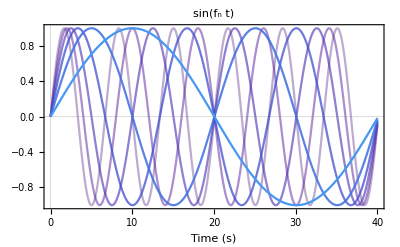

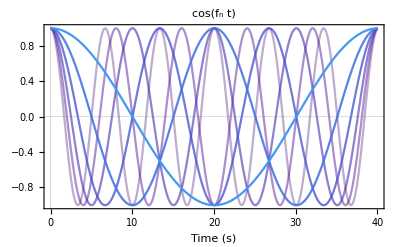

```mathematica
ptsSin=Table[Transpose[{dataDesc["times"]-dataDesc["times"][[1]],Table[Sin[freq*(t-1)],{t,1,dataDesc["noTpts"]}]}],{freq,Reverse[freqs["rxns"]]}];
ptsCos=Table[Transpose[{dataDesc["times"]-dataDesc["times"][[1]],Table[Cos[freq*(t-1)],{t,1,dataDesc["noTpts"]}]}],{freq,Reverse[freqs["rxns"]]}];
pltSin=ListLinePlot[ptsSin,PlotStyle->colors,FrameLabel->{"Time (s)"},PlotLabel->"sin(f_n t)"]
pltCos=ListLinePlot[ptsCos,PlotStyle->colors,FrameLabel->{"Time (s)"},PlotLabel->"cos(f_n t)"]

leg=LineLegend[Reverse[colors],{"1 x (2π/40)","2 x (2π/40)","3 x (2π/40)","4 x (2π/40)","5 x (2π/40)","6 x (2π/40)"}]

SetDirectory[NotebookDirectory[]];
Export["figures/fourier/freqs_sin.pdf",pltSin];
Export["figures/fourier/freqs_cos.pdf",pltCos];
Export["figures/fourier/freqs_leg.pdf",leg];
```